```mathematica
(* Set directory is required for each cold start. Modify this to your dir. *)
SetDirectory["/Users/plumbus/Projects/astro"];
```

```mathematica
areaFiles = FileNames["./bench/run/area-*.json"];
```

```mathematica
areaJSON = Import[#1]&/@areaFiles;
areaJSONValues = Transpose@Values@areaJSON;
```

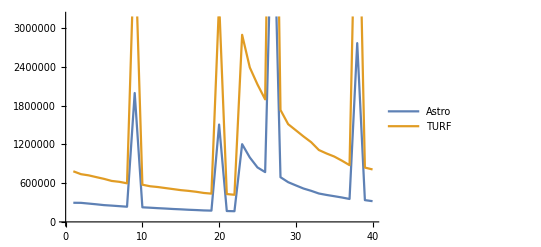

```mathematica
(* Show plot of ops/sec - higher is better - in relation to n polygon size. *)
ListLinePlot[areaJSONValues, PlotLegends->{"Astro", "TURF"}]
```

```mathematica
astroMean = Mean[areaJSONValues[[1]]]
```

637779.

```mathematica
turfMean = Mean[areaJSONValues[[2]]]
```

1.46712×10^6